# Homework 3

## Exercise 1

## Part (i)

```mathematica
(* Func draws from standard normal N(0,1) using Box-Muller*)
drawStandardNormal[]:= Module[{Y},
(* Box-Muller method *)
Y =   Sqrt[-2 Log[RandomReal[]]]*Sin[2*Pi * RandomReal[]];
Y
]
```

```mathematica
(* Func draws from the given bivariate normal N_2(b,(4 -1, -1 4)) *)
drawBivariateNormal[b_,delta_]:= Module[{X},
Y=Table[drawStandardNormal[],3];
X = b+Sqrt[delta]{Sqrt[3]*Y[[1]]+Y[[3]], Sqrt[3]*Y[[2]]-Y[[3]]};
X
]
```

```mathematica
(* Func uses R replications in CMC to estimate z=P(X in A_a) with a 95% CI*)
doCrudeMonteCarlo[a_,R_] := Module[{z,CI},
(* Generate R replicates of Z=1_A(X) *)
X = Table[drawBivariateNormal[0,1],R];
indicatorFunc[{x1_,x2_}]:= Boole[x1≥ a && x2 ≥ a];
Z = indicatorFunc /@ X;

(* Estimate z *)
z = Mean[Z];
(* Calculate the CI *)
s = Sqrt[Variance[Z]];
CI = {z-1.96*s/Sqrt[R], z+1.96*s/Sqrt[R]};
{z,CI}
]
```

```mathematica
doCrudeMonteCarlo[1,100000]
doCrudeMonteCarlo[3,100000]
doCrudeMonteCarlo[10,100000]
```

{6441/100000,{0.0628885,0.0659315}}

{3/2000,{0.00126013,0.00173987}}

{0,{0.,0.}}

## Part (ii)

```mathematica
Minimize[{2x1^2-x1 x2 + 2x2^2,x1≥a,x2≥a},{x1,x2}]
```

{Piecewise[{{3 a^2, a>0}, {0, True}}],{x1→Piecewise[{{a, a>0}, {0, True}}],x2→Piecewise[{{1/4 (a+3 √(a^2)), a>0}, {0, True}}]}}

```mathematica
(* Likelihood ratio function *)
L1[a_,x_]:= Exp[-{a,a}.Inverse[{{4,-1},{-1,4}}].x+1/2 *{a,a}.Inverse[{{4,-1},{-1,4}}].{a,a}];
```

```mathematica
(* Func estimates z with importance sampling of R replicates where importance distribution is N((a,a),C)*)
doImportanceSampling[a_,R_] := Module[{z,CI},
(* Generate R replicates of Z=1_A(X)L(X) *)
X = Table[drawBivariateNormal[{a,a},1],R];
indicatorAndLFunc[{x1_,x2_}]:= Boole[x1≥ a && x2 ≥ a]*L1[a,{x1,x2}];
Z = indicatorAndLFunc/@ X;

(* Estimate z *)
z = Mean[Z];
(* Calculate the CI *)
s = Sqrt[Variance[Z]];
CI = {z-1.96*s/Sqrt[R], z+1.96*s/Sqrt[R]};
{z,CI}
]
```

```mathematica
doImportanceSampling[1,100000]
doImportanceSampling[3,100000]
doImportanceSampling[10,100000]
```

{0.0645238,{0.063652,0.0653956}}

{0.00136031,{0.00133264,0.00138798}}

{1.17023×10^-17,{1.10825×10^-17,1.23221×10^-17}}

## Part (iii)

```mathematica
(* Likelihood ratio function *)
L2[a_,x_,delta_]:=Module[{L},
invC= Inverse[{{4,-1},{-1,4}}];
b={a,a};
L=delta*Exp[-1/2x.invC.x+1/(2delta)x.invC.x-1/delta x.invC.b+1/(2delta)b.invC.b];
L
]
```

```mathematica
(* Func estimates z with importance sampling of R replicates where importance distribution is N((a,a),delta C)*)
doImportanceSampling2[a_,R_,delta_] := Module[{z,CI},
(* Generate R replicates of Z=1_A(X)L(X) *)
X = Table[drawBivariateNormal[{a,a},delta],R];
indicatorAndLFunc[{x1_,x2_}]:= Boole[x1≥ a && x2 ≥ a]*L2[a,{x1,x2},delta];
Z = indicatorAndLFunc/@ X;

(* Estimate z *)
z = Mean[Z];
(* Calculate the CI *)
s = Sqrt[Variance[Z]];
CI = {z-1.96*s/Sqrt[R], z+1.96*s/Sqrt[R]};
{z,CI}
]
```

```mathematica
doImportanceSampling2[1,100000,1]
doImportanceSampling2[3,100000,1]
doImportanceSampling2[10,100000,1]
```

{0.0651362,{0.064258,0.0660144}}

{0.00138812,{0.00135993,0.00141631}}

{1.17655×10^-17,{1.11393×10^-17,1.23917×10^-17}}

```mathematica
doImportanceSampling2[10,100000,1]
```

{1.1555×10^-17,{1.09352×10^-17,1.21749×10^-17}}

General::munfl: Exp[-813.821] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.313] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-887.745] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

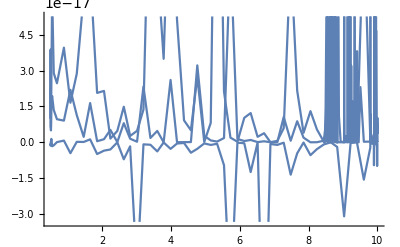

```mathematica
result = Table[doImportanceSampling2[10,100,delta],{delta,0.5,100,0.5}];
Plot[doImportanceSampling2[10,100,delta],{delta,0.5,10}]
```

## Exercise 3

## Part 1

```mathematica
(* Func does CMC with R replications *)
doCMC[R_] := Module[{z},
z = Mean[Table[Boole[Product[RandomReal[],{i,20}]≥ Exp[-15/(0.5+RandomReal[])]],R]];
z
]
N[doCMC[1000]]
```

0.298

```mathematica
varCMC = N[Variance[Table[doCMC[1000],100]]]
```

0.000223687

## Part 2

```mathematica
(* Func generates Z and a control variate W *)
generateZandW[]:= Module[{Z,W},
W=Sum[Log[RandomReal[]],{i,20}];
Z=CDF[UniformDistribution[{0,1}],-15/W-0.5];
{Z,W}
]
```

```mathematica
(* Func provides the control variate estimator with R replications *)
simulateControlVariate[R_]:= Module[{ZandW,Z,W,estimate},
ZandW= Table[generateZandW[],R];
Z = ZandW[[All,1]];
W = ZandW[[All,2]];
estimate = Mean[Z]-Covariance[Z,W]/Variance[W](Mean[W]+20);
estimate
]
simulateControlVariate[1000]
```

0.292101

```mathematica
varControlVariateSim = N[Variance[Table[simulateControlVariate[1000],100]]]
```

4.20094×10^-6

## Part 3

```mathematica
(* generates vector [Z_1,...,Z_R/2, ..., Z_R] with antithetic second half *)
generateZ[]:=Module[{U,Z,antitheticZ},
U=Table[RandomReal[{0,1}],20];
Z=CDF[UniformDistribution[{0,1}],-15/Sum[Log[U[[i]]],{i,20}]-0.5];
antitheticZ = CDF[UniformDistribution[{0,1}],-15/Sum[Log[1-U[[i]]],{i,20}]-0.5];
{Z,antitheticZ}
]
```

```mathematica
(* simulates using antithetic variables *)
antitheticSimulation[R_]:= Module[{z},
z=Mean[Mean[Table[generateZ[],R/2]]];
z
]
antitheticSimulation[1000]
```

0.283359

```mathematica
varAntithetic = N[Variance[Table[antitheticSimulation[1000],100]]]
```

0.0000137377

## Exercise 5

## Control Variate

```mathematica
X = Table[RandomVariate[ExponentialDistribution[1]],10];
Z = Table[(x+0.02x^2)Exp[0.1Sqrt[1+Cos[x]]] ,{x,X}];
W = Table[(x+0.02x^2)Exp[0.1],{x,X}];
Correlation[Z,W]
```

0.998759

```mathematica
Integrate[(x+0.02x^2)Exp[0.1-x],{x,0,Infinity}]
```

1.14938

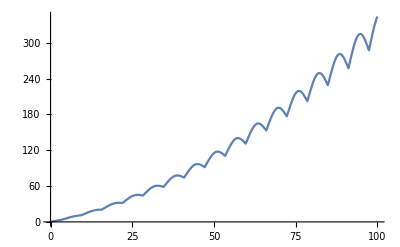

```mathematica
Plot[(x+0.02x^2)Exp[0.1Sqrt[1+Cos[x]]],{x,0,100}]
```